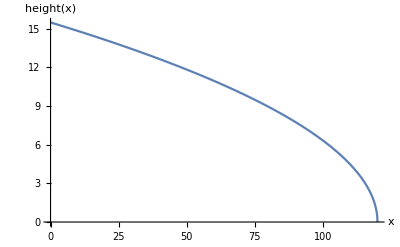

```mathematica
b=6;
L=120;
σ=1;
ρ=2*^-5;
P=2;
h[x_]:=Sqrt[6*P*(L-x) / (σ * b)];
Plot[h[x],{x,0,L}, AxesLabel->{"x","height(x)"}]
```

```mathematica
h[0] //N
h[L]
```

15.4919

0

```mathematica
b * Integrate[h[x],{x,0, L}] //N
```

7436.13

```mathematica
ρ*b * Integrate[h[x],{x,0, L}] //N
```

0.148723